# Simpson’s Rule Created by Haroon Sakhi

## ✨ Introduction

Simpson’s Rule is a numerical integration technique that approximates the area under a curve by fitting parabolas to segments of the curve. Although the rule is often attributed to Thomas Simpson, it was originally developed by Johannes Kepler in 1671, referred to as Keplersche Fassregel in German. Simpson further refined this method in the early 1700s.
There are two primary variants of Simpson’s Rule: the 1/3rd rule and the 3/8th rule. The 3/8 rule offers improved error bounds but maintains the same order of error. The key advantage of Simpson’s Rule lies in its parabolic approximation, which can more accurately model nonlinear curves compared to linear methods like the Trapezoidal Rule.

## 🔢 Problem Setup

Consider a function  defined over the domain .

-Graphics-

Figure 1: An arbitrary curve.

We discretize the domain into  intervals. For each subinterval, three points, , are selected. Using these points, we fit a parabola described by the general equation:

The coefficients  are determined by solving a system of equations based on the selected points.  A  visualization of this process is shown in Fig. 2.

-Graphics-
 Figure 2: Discretization of the domain.

For the first three points, the equation of the fitted parabola is:

We then compute the area under this parabola for the first three intervals. The approximation error is visualized, where the purple area represents the approximate area under the parabola, while the red-shaded and green-shaded regions correspond to the overestimation and underestimation, respectively. These errors tend to cancel out, providing a more accurate result than linear approximations.

## 📍 Generalized Expression

To find the area under a parabola:

We compute the definite integral over the domain  :

Using three neighboring points in the domain  using above equation:

-Graphics-

Figure 3: Approximation error for the first three intervals.

Summing these values:

We can see a very interesting observation. Factoring out  from above equation we can see it takes the form

We can express the area under a parabola as:

Applying this to the entire domain:

Thus, the general Simpson’s Rule formula is:

## 🛠️ Algorithm

Using the formula, the area can be computed as follows:

Define the domain and discretize it into  intervals.

Ensure that  is ; if not, adjust .

Assign weights to the function values:

Multiply function values by  if the index is .

Multiply function values by  if the index is .

Use the formula to compute the total area.

## 📌 Example Problem

### 🔷 Defining the Function .

Consider the function:

```mathematica
FunctionF[x_]:=0.4*Sin[0.8*(x*x)]+2
```

#### 📊 Visualization

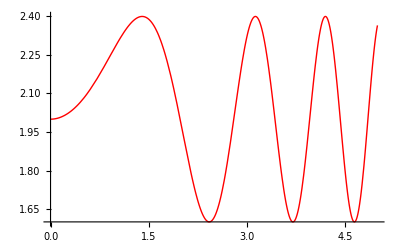

```mathematica
Plot[0.4*Sin[0.8*(x*x)]+2,{x,0,5},PlotStyle->{Thick,Red}]
```

### 🔷 Implement Simpson’s Rule

```mathematica
SimpsonsRule[start_,end_,numIntervals_]:=Module[{h,x,y0,yn,K,i,area,intervals},
(*Ensure the number of intervals is even*)
intervals=If[OddQ[numIntervals],numIntervals+1,numIntervals];
h=(end-start)/intervals;
x=start+h;
y0=FunctionF[start];
yn=FunctionF[end];
K=0;
For[i=1,i<intervals,i++,If[EvenQ[i],K+=2*FunctionF[x],K+=4*FunctionF[x]];
x+=h;];
area=(h/3.0)*(y0+K+yn);
area]
```

### 🔷 Integration Limits

```mathematica
xi=0;
xf=5;
numIntervals=10000;
```

### 🔷 Compute the area and error

```mathematica
exactValue=10.2588;
computedArea=SimpsonsRule[xi,xf,numIntervals];
error=Abs[(computedArea-exactValue)/exactValue]*100;
```

### 📊 Results

```mathematica
Print["Area: ",NumberForm[computedArea,{6,4}]];
Print["Error: ",NumberForm[error,{6,4}]];
```

Area: 10.2588

Error: 0.0005

## 🎯 Conclusion

Simpson’s Rule is highly effective for approximating the integral of nonlinear curves due to its use of parabolas to estimate the area under the curve. It also performs well for linear functions, as a straight line can be viewed as a special case of a parabola. A critical requirement for applying Simpson’s Rule is that the domain must be divided into an even number of intervals, as the method fits parabolas to groups of three points.
              However, Simpson’s Rule struggles with highly oscillatory functions and may not accurately approximate non-polynomial functions, potentially leading to errors in the final result.